# Sign

info@cafeplanck.com

```mathematica
Sign[x]//TraditionalForm
```

sgn(x)

```mathematica
PiecewiseExpand[Sign[x],-3<x<3]
```

Piecewise[{{-1, x<0}, {1, x>0}, {0, True}}]

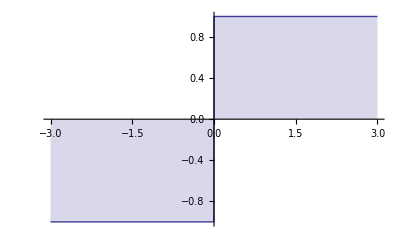

```mathematica
Plot[Sign[x],{x,-3,3},Filling->Axis]
```

```mathematica
Integrate[Sign[x],x,Assumptions->x∈Reals]
```

Piecewise[{{-x, x≤0}, {x, True}}]

```mathematica
FourierTransform[Sign[y],y,x]
```

(ⅈ √(2/π))/x

```mathematica
LaplaceTransform[Sign[y],y,x]
```

1/x